```mathematica
(*X=10 Y=0.5 Yielding Physical states (and subsequently 3-entangled states) for t between 0 and 2pi*)
```

```mathematica
Table[Eigs[[1]],{t,0,2π,π/100}];
```

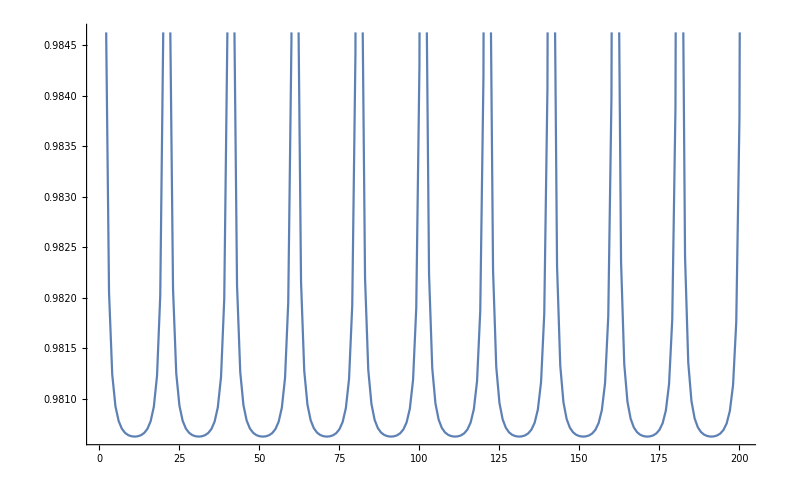

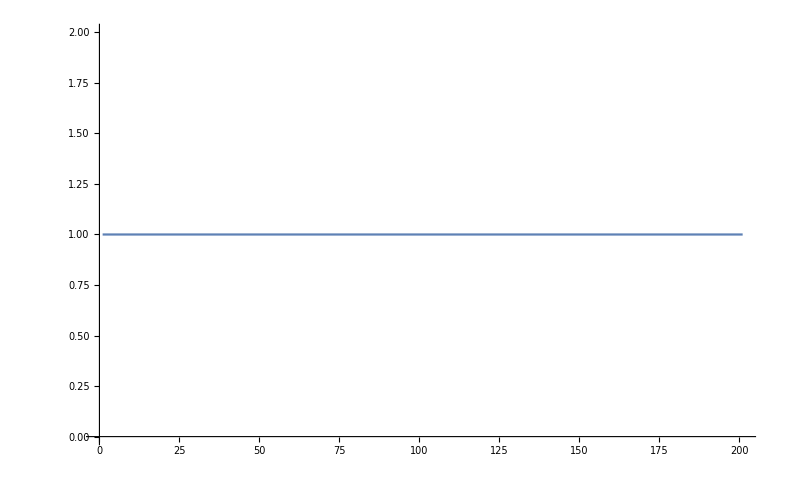

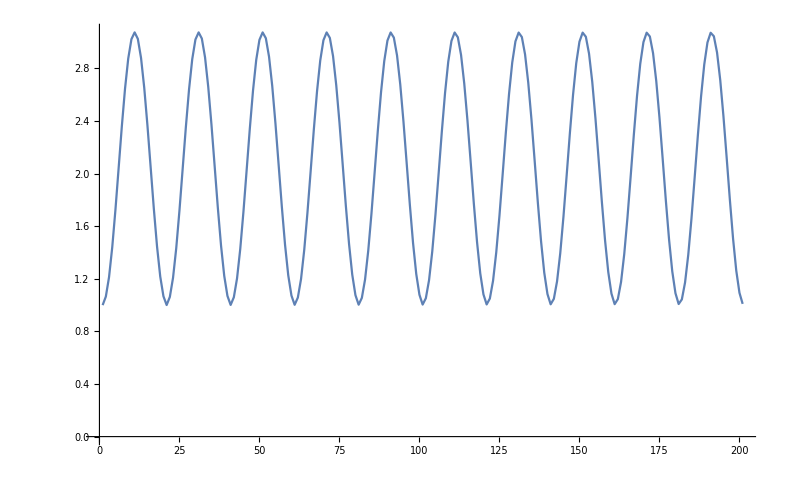

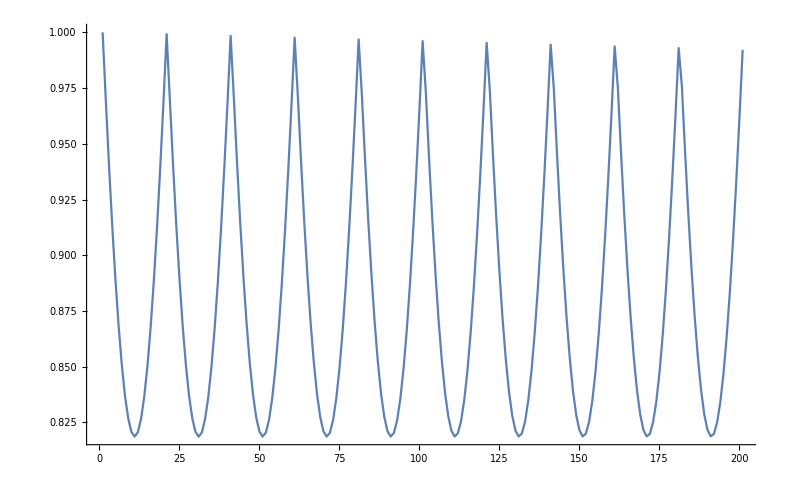

-Graphics-

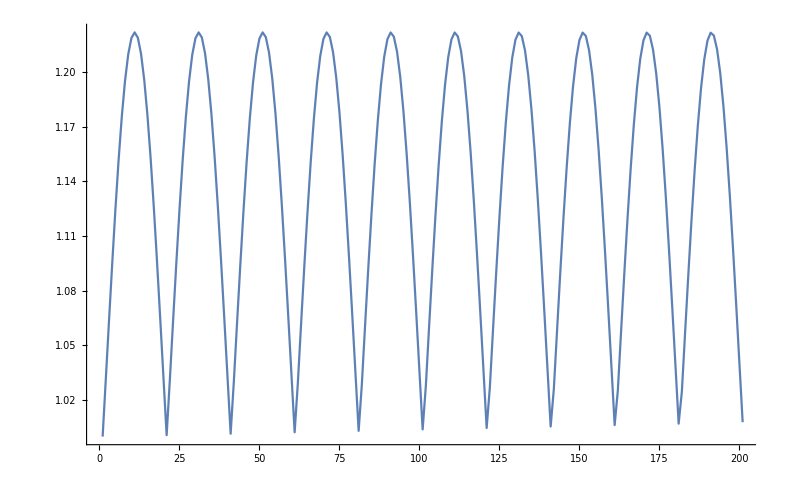

```mathematica
ListPlot[Table[Eigs[[1]],{t,0,2π,π/100}],Joined->True]
ListPlot[Table[Eigs[[2]],{t,0,2π,π/100}],Joined->True]
ListPlot[Table[Eigs[[3]],{t,0,2π,π/100}],Joined->True]
ListPlot[Table[Eigs[[4]],{t,0,2π,π/100}],Joined->True]
ListPlot[Table[Eigs[[5]],{t,0,2π,π/100}],Joined->True]
ListPlot[Table[Eigs[[6]],{t,0,2π,π/100}],Joined->True]
(*Checking first condition for Bona Fide C.M.; These eigenfunctions should be greater than 0 to be physical*)
```

```mathematica
Show[%843,PlotLabel->None,LabelStyle->{12,RGBColor[1.,0.9999694819562066,0.9999847409781033]}]
```

-Graphics-

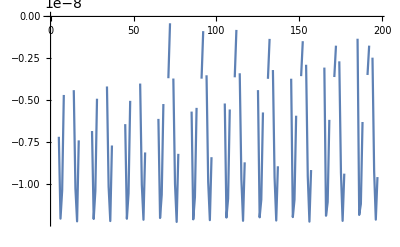

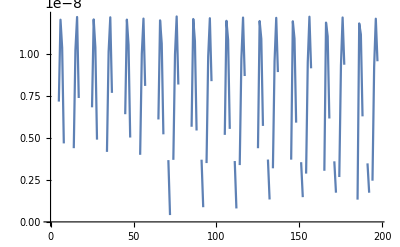

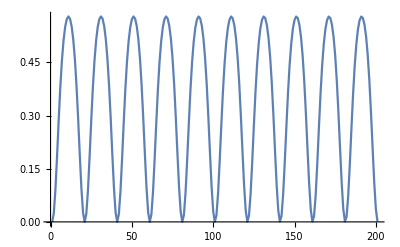

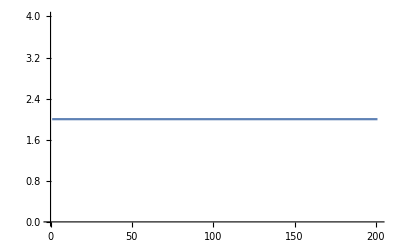

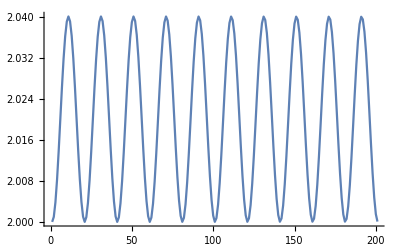

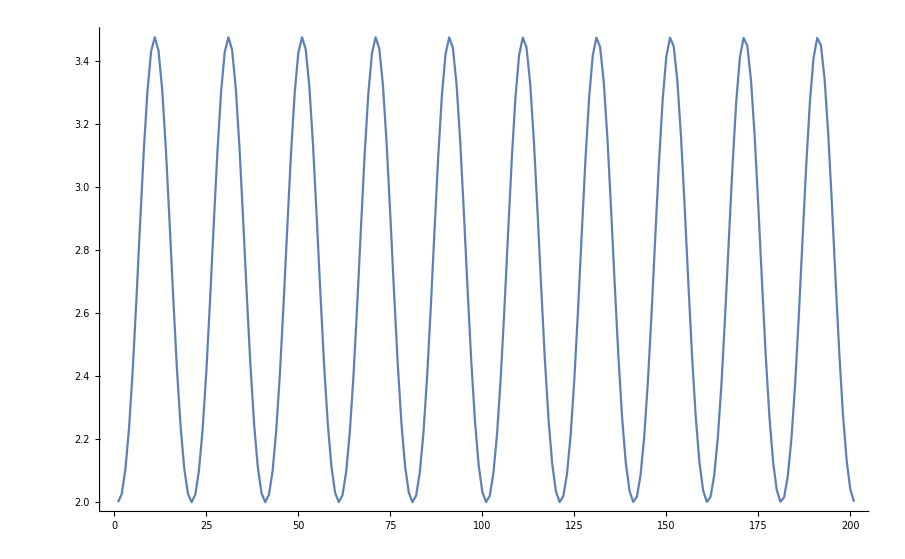

```mathematica
EigSymp=Eigenvalues[σ+ⅈ Σ];
ListPlot[Table[EigSymp[[1]],{t,0,2π,π/100}],Joined->True]
ListPlot[Table[EigSymp[[2]],{t,0,2π,π/100}],Joined->True]
ListPlot[Table[EigSymp[[3]],{t,0,2π,π/100}],Joined->True]
ListPlot[Table[EigSymp[[4]],{t,0,2π,π/100}],Joined->True]
ListPlot[Table[EigSymp[[5]],{t,0,2π,π/100}],Joined->True]
ListPlot[Table[EigSymp[[6]],{t,0,2π,π/100}],Joined->True]
(*Checking second condition for Bona Fide C.M.; These eigenfunctions should be also greater than 0 to be physical*)
```

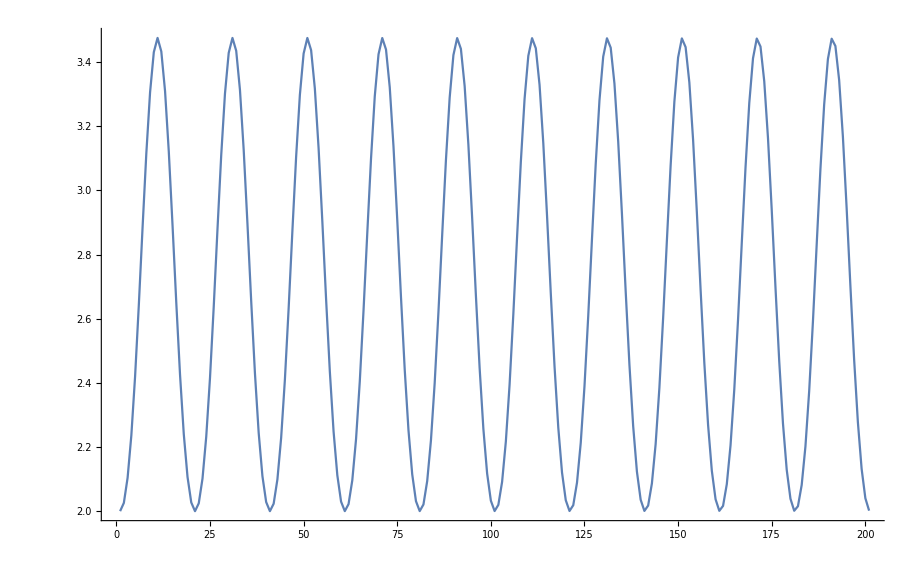

```mathematica
Show[%887,PlotLabel->None,LabelStyle->{16,RGBColor[1.,0.9999694819562066,0.9999847409781033]}]
```

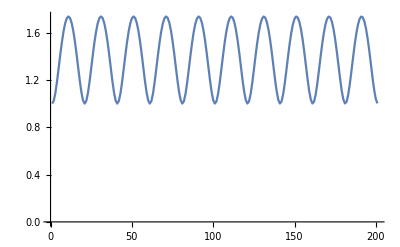

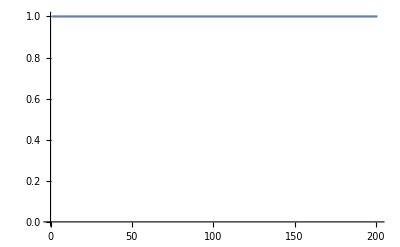

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
SympEig=Eigenvalues[ⅈ Σ . σ];
ListPlot[Table[Abs[SympEig[[1]]],{t,0,2π,π/100}],Joined->True,PlotRange->{0,Automatic}]
ListPlot[Table[Abs[SympEig[[2]]],{t,0,2π,π/100}],Joined->True,PlotRange->{0,Automatic}]
ListPlot[Table[Abs[SympEig[[3]]],{t,0,2π,π/100}],Joined->True,PlotRange->{0,Automatic}]
ListPlot[Table[Abs[SympEig[[4]]],{t,0,2π,π/100}],Joined->True,PlotRange->{0,Automatic}]
ListPlot[Table[Abs[SympEig[[5]]],{t,0,2π,π/100}],Joined->True,PlotRange->{0,Automatic}]
ListPlot[Table[Abs[SympEig[[6]]],{t,0,2π,π/100}],Joined->True,PlotRange->{0,Automatic}]
(*Checking third condition for Bona Fide C.M.; These eigenfunctions should be also greater than or equal 1 (not zero) to be physical*)
```

```mathematica
V1=Table[Min[Abs[Eigenvalues[ⅈ Σ . σPT1]]],{t,0,2π,π/200}];
V2=Table[Min[Abs[Eigenvalues[ⅈ Σ . σPT2]]],{t,0,2π,π/200}];
V3=Table[Min[Abs[Eigenvalues[ⅈ Σ . σPT3]]],{t,0,2π,π/200}];
```

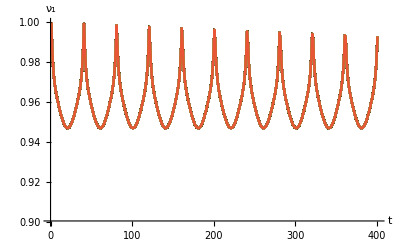

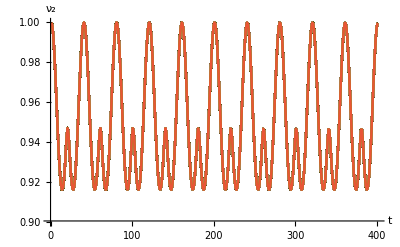

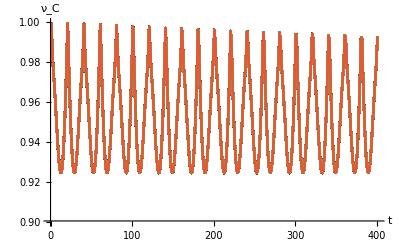

```mathematica
ListPlot[Table[V1,{t,0,2π,π/200}],Joined->True,PlotRange->{0.9,Automatic},AxesLabel->{t,Subscript[ν, 1]}]
ListPlot[Table[V2,{t,0,2π,π/200}],Joined->True,PlotRange->{0.9,Automatic},AxesLabel->{t,Subscript[ν, 2]}]
ListPlot[Table[V3,{t,0,2π,π/200}],Joined->True,PlotRange->{0.9,Automatic},AxesLabel->{t,Subscript[ν, C]}]
```

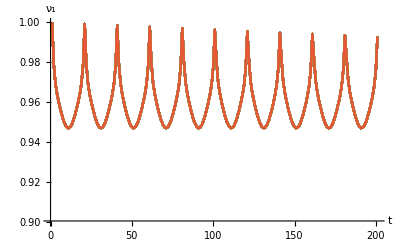

```mathematica
Show[%926,PlotLabel->None,LabelStyle->{16,RGBColor[1.,0.9999694819562066,0.9999847409781033]}]
```